```mathematica
(*单个点电荷*)
```

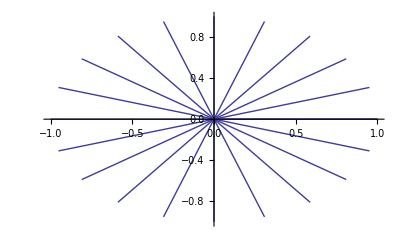

```mathematica
ϕ[x_,y_]:=1/(√(x^2+y^2));
Ex=-D[ϕ[x,y],x];
Ey=-D[ϕ[x,y],y];
k=(Ey/Ex)/.y->y[x];
r=10.0^-3;R=1.0;forceline={};
eqs={y'[x]==k,y[xst]==yst};
Do[xst=r*Cos[θ];yst=r*Sin[θ];xnd=R*Cos[θ];
s=NDSolve[eqs,y,{x,xst,xnd}];y=y/.s[[1]];figure=Plot[y[x],{x,xst,xnd}];AppendTo[forceline,figure];Clear[y],{θ,0.0,2π,π/10.0}]
Show[forceline,PlotRange->All]
```

```mathematica
Clear[ϕ,Ex,Ey,k,r,R,forceline,y,xst,yst,xnd,s,figure,eqs]
```

```mathematica
(*两个点电荷*)
```

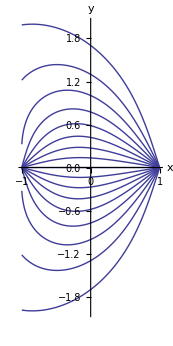

```mathematica
r=10.0^-3;a=1.0;q1=1.0;q2=-0.4;
ϕ[x_,y_]:=q1/(√((x-a)^2+y^2))+q2/(√((x+a)^2+y^2));
Ex=-D[ϕ[x,y],x];
Ey=-D[ϕ[x,y],y];
k=(Ey/Ex)/.y->y[x];
forceline={};
θ1=π/2.0+π/10.0;θ2=3π/2.0-π/10.0;
eqs={y'[x]==k,y[xst]==yst};
Do[xst=a+r*Cos[θ];yst=r*Sin[θ];xnd=-(a-r*Cos[π-θ]);
s=NDSolve[eqs,y,{x,xst,xnd}];y=y/.s[[1]];figure=Plot[y[x],{x,xst,xnd},AspectRatio->Automatic];AppendTo[forceline,figure];Clear[y],{θ,θ1,θ2,π/20.0}]
Show[forceline,PlotRange->All,AxesLabel->{"x","y"}]
```

```mathematica
Clear[r,a,q1,q2,ϕ,Ex,Ey,k,forceline,θ1,θ2,eqs,y,xst,yst,xnd,figure,s]
```

```mathematica
(*折线法*)
```

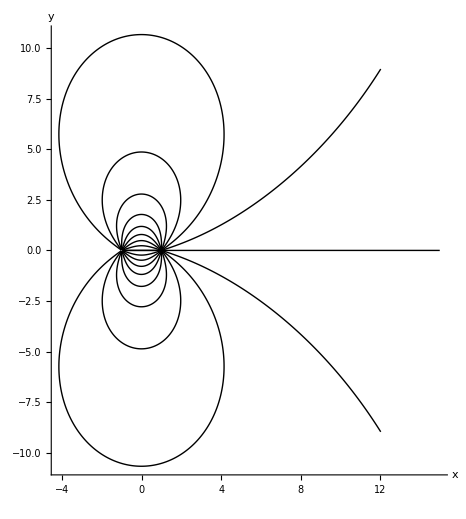

```mathematica
p1={1,0};p2={-1,0};q1=1.0;q2=-1.0;
ψ=q1/(√((x-1)^2+y^2))+q2/(√((x+1)^2+y^2));
field=-D[ψ,x]-ⅈ*D[ψ,y];
step=0.03;r1=0.02;r2=15;forceline={};
Do[θ=ϕ;single={p1};
Label[ss];p=Last[single];p=p+step*{Cos[θ],Sin[θ]};θ=Arg[field/.{x->p[[1]],y->p[[2]]}];
If[(Norm[p-p1]>r1)∧(Norm[p-p2]>r1)∧(Norm[p]<r2),AppendTo[single,p];Goto[ss]];AppendTo[forceline,single],{ϕ,-π,π,π/10}]
Show[Graphics[{Line/@forceline}],Axes->True,PlotRange->All,AspectRatio->Automatic,AxesLabel->{"x","y"}]
```

```mathematica
Clear[p1,p2,p3,q1,q2,q3,ψ,field,step,r1,r2,forceline,θ,single,p]
```

```mathematica
(*三电荷试玩*)
```

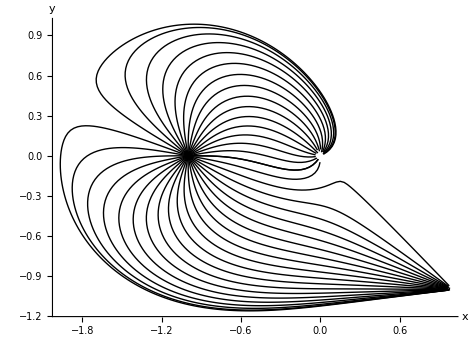

```mathematica
p1={0,0};p2={-1,0};p3={1,-1};q1=1.0;q2=-3.0;q3=30.0;
ψ[x_,y_]:=q1/(√((x-0)^2+y^2))+q2/(√((x+1)^2+(y-0)^2))+q3/(√((x-1)^2+(y+1)^2));
field=-D[ψ[x,y],x]-ⅈ*D[ψ[x,y],y];
step=0.03;r1=0.02;r2=15;forceline={};
Do[θ=ϕ;single={p2};
Label[ss];p=Last[single];p=p-step*{Cos[θ],Sin[θ]};θ=Arg[field/.{x->p[[1]],y->p[[2]]}];
If[(Norm[p-p1]>r1)∧(Norm[p-p2]>r1)∧(Norm[p-p3]>r1)∧(Norm[p]<r2),AppendTo[single,p];Goto[ss]];AppendTo[forceline,single],{ϕ,-π,π,π/18}]
Show[Graphics[{Line/@forceline}],Axes->True,PlotRange->All,AspectRatio->Automatic,AxesLabel->{"x","y"}]
```

```mathematica
(*参数方程法*)
```

NDSolve::evre: The value of the event function at t = 6.69492×10^-15 was not a real number. The event will be ignored in steps where it does not evaluate to real numbers at both ends.

NDSolve::ndsz: At t == 0.463863, step size is effectively zero; singularity or stiff system suspected.

NDSolve::evre: The value of the event function at t = 6.7758×10^-15 was not a real number. The event will be ignored in steps where it does not evaluate to real numbers at both ends.

NDSolve::ndsz: At t == 0.342024, step size is effectively zero; singularity or stiff system suspected.

NDSolve::evre: The value of the event function at t = 7.02998×10^-15 was not a real number. The event will be ignored in steps where it does not evaluate to real numbers at both ends.

General::stop: Further output of NDSolve :: evre will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.261914, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

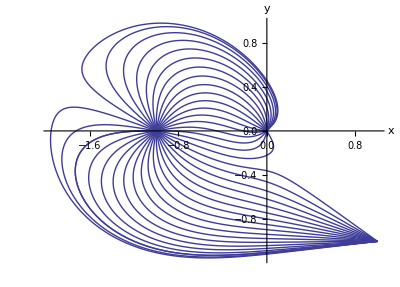

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
p1={0,0};p2={-1,0};p3={1,-1};q1=1.0;q2=-3.0;q3=30.0;
ψ[x_,y_]:=q1/(√((x-0)^2+y^2))+q2/(√((x+1)^2+(y-0)^2))+q3/(√((x-1)^2+(y+1)^2));
Ex[t_]:=Evaluate[D[ψ[x,y],x]/.{x->x[t],y->y[t]}];
Ey[t_]:=Evaluate[D[ψ[x,y],y]/.{x->x[t],y->y[t]}];
eqs={x'[t]==Ex[t],y'[t]==Ey[t],x[0]==x0,y[0]==y0};
r=10.0^-3;forceline={};
Do[{x0,y0}=p2+r*{Cos[ϕ],Sin[ϕ]};s=NDSolve[eqs,{x,y},{t,0,∞},
Method->{"EventLocator","Event"->Norm[{x[t],y[t]}-p1]-r∨Norm[{x[t],y[t]}-p3]-r}];
end=InterpolatingFunctionDomain[First[y/.s]][[1,-1]];
g=ParametricPlot[Evaluate[{x[t],y[t]}/.First[s]],{t,0,end}];AppendTo[forceline,g],{ϕ,-π,π,π/18.0}]
Show[forceline,PlotRange->All,AxesLabel->{"x","y"}]
```